{{phi→InterpolatingFunction[…],alpha→InterpolatingFunction[…]}}

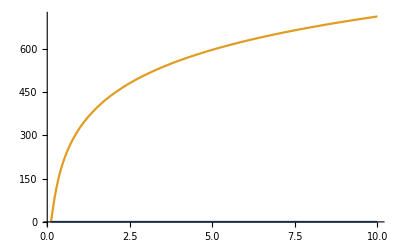

g'[h[x]] h'[x]

```mathematica
(* Simple example case where alpha is a constant = pi/2, no z derivatives: *)

s = NDSolve[{K*u*((u^3)*D[phi[u],u]+D[phi[u],u,u]*(u^4)+(1/2)*(u^2)*Sin[2*phi[u]])==0,phi[.001]==0,(D[phi[u],u]/.u->.001)==.001},phi,{u,10,.001}];
Plot[Evaluate[phi[u]/.s],{u,10,.001},PlotRange->All]; 

(* u*((Sin[phi[u]]^2)*(u^3)*D[alpha[u],u]+(Sin[phi[u]]^2)*(u^4)*D[alpha[u],u,u]+Sin[2*phi[u]]*(u^4)*D[phi[u],u]*D[alpha[u],u]+(1/2)*(u^2)*Sin[2*alpha[u]]*(Sin[phi[u]])^2 )+(1/2)*(Cos[2*alpha[u]]-1)*(Sin[phi[u]]^2) ==0 *)
s = NDSolve[{u*((u^3)*D[phi[u],u]+D[phi[u],u,u]*(u^4)+(1/2)*(u^2)*Sin[2*phi[u]]*(Sin[alpha[u]]^2)-Sin[phi[u]]*Cos[phi[u]]*(u^2))+(1/4)*Sin[2*alpha[u]]*Sin[2*phi[u]]+Sin[2*phi[u]]*(u^4)*D[phi[u],u]*D[alpha[u],u]==0,(Sin[phi[u]]^2)*(u^4)*D[alpha[u],u]+(Sin[phi[u]]^2)*(u^5)*D[alpha[u],u,u]+(1/2)*(u^3)*Sin[2*alpha[u]]*(Sin[phi[u]])^2 +(1/2)*(Cos[2*alpha[u]]-1)*(Sin[phi[u]]^2)==0,phi[1/10]==0,(D[phi[u],u]/.u->1/10)==1/10,(D[alpha[u],u]/.u->1/10)==1/10,alpha[1/10]==1/2},{phi,alpha},{u,10,1/10}] 
Plot[Evaluate[{phi[u],alpha[u]}/.s, {u,10,1/10}]]
D[g[h[x]],x]
```